```mathematica
$Assumptions = x1 ∈Reals&& x2∈Reals&&x3∈Reals&&x4 ∈Reals&& s∈Reals;
ϕ[x1_,x2_,s_] = x1^2 + (x2 - s)^2;
```

x1∈ℝ&&x2∈ℝ&&x3∈ℝ&&x4∈ℝ&&s∈ℝ

x1^2+(-s+x2)^2

```mathematica
Dϕ = D[ϕ[x1,x2,s],{{x1,x2}}];
Dϕinverse=Dϕ/Norm[Dϕ]^2//FullSimplify ;
```

(x1/(2 (x1^2+(s-x2)^2))
(-s+x2)/(2 (x1^2+(s-x2)^2)))

```mathematica
ϕ' = (D[ϕ[x1,x2,s[t]],t])/.{s'[t] -> s', s[t]->s};
ϕ'' = (D[ϕ[x1,x2,s[t]],{t,2}])/.{s'[t] -> s', s[t]->s};
```

```mathematica
v = Simplify[- Dϕinverse ϕ',x1^2 + (x2 - s)^2==1]/.{s'->p};
v = v/.{s->x2-Sqrt[1-x1^2]};
Solve[v[[1]]^2+v[[2]]^2==1&&0<=x1<1,p]//Simplify
```

{p x1 √(1-x1^2),-p (-1+x1^2)}

{{p→ConditionalExpression[-1/(√(1-x1^2)), 0<x1<1]},{p→ConditionalExpression[1/(√(1-x1^2)), 0<x1<1]}}

```mathematica
v/.{p->1/Sqrt[1-x1^2]}//Simplify
```

{x1,√(1-x1^2)}

```mathematica
sols = Table[
DSolve[x1'[t] == x1[t]&&x2'[t]==√(1-x1[t]^2)&&x1[0]==Cos[θ]&&x2[0]==Sin[θ],{x1[t],x2[t]},t][[1]],{θ,0,Pi,Pi/100}];
```

DSolve::bvnul: For some branches of the general solution, the given boundary conditions lead to an empty solution.

Part::partw: Part 1 of {} does not exist.

```mathematica
f = Table[
ListLinePlot[
Table[{x1[t],x2[t]}/.sols[[n]]/.{t->τ},{n,1,Length[sols]}
],
PlotStyle->Gray
],
{τ,-.5,.5,.05}
];
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
refcurve = ListLinePlot[
Table[{x1[t],x2[t]}/.sols[[n]]/.{t->0},{n,1,Length[sols]}],PlotStyle->Red
];
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

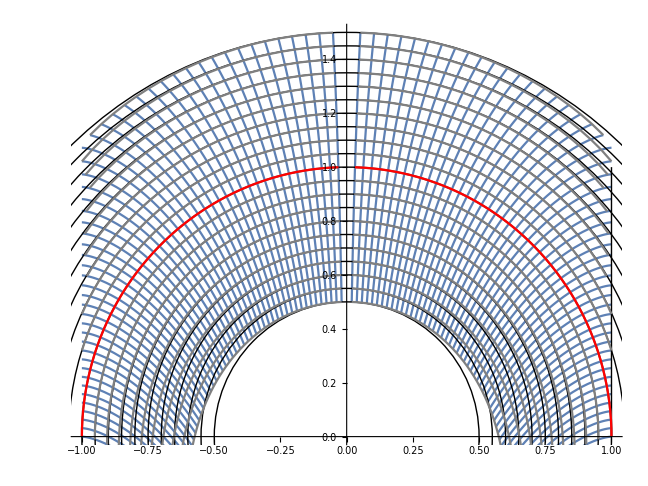

```mathematica
Show[
Table[
ParametricPlot[
{x1[t],x2[t]}/.sols[[n]],{t,-.5,.5},
Background->White,
PlotRange->{{-1,1},{0,1.5}}
],
{n,1,Length[sols]}
],
Table[Graphics[Circle[{0,0},n]],{n,.5,1.5,.05}],
Graphics[Line[
{{1,0},{1,1}}
]
],
f,refcurve
]
```

```mathematica
k = Table[
D[{x1[t],x2[t]}/.sols[[n]],{t,2}],{n,1,Length[sols]}]/.{t->0}//N;
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Power::infy: Infinite expression 1/0^(3/2) encountered.

Power::infy: Infinite expression 1/(√0) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::ivar: 0 is not a valid variable.

Infinity::indet: Indeterminate expression ComplexInfinity+ComplexInfinity+ComplexInfinity encountered.

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

D::dvar: Multiple derivative specifier {0.,2.} does not have the form {variable, n}, where n is symbolic or a non-negative integer.

{0.960294,-3.30535}

```mathematica
Show[Table[
ParametricPlot[
{x1[t],x2[t]}/.sols[[n]],{t,-.5,.5},
Background->White,
PlotRange->{{-1,1},{0,1.5}}
],
{n,1,Length[sols],5}
], 
refcurve,
Epilog->Table[
Arrow[
{
{x1[t],x2[t]},
{x1[t],x2[t]}-.5 (k[[n]])
}/.{sols[[n]]}]
,{n,1,Length[sols],5}]/.{t->0}
]
```

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

ReplaceAll::reps: {{}⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

{{Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}],Arrow[{{{1,0},{1,1}}}]},99,{Arrow[{{{-1,0},{-1,-1}}}],8,Arrow[{1}]}}
 |  |  |  |